```mathematica
(*generate tone row*)
A pitch-class set is a set of distinct integers representing pitch classes.
Order doesn't matter for unordered sets
Cardinal number of a set - number of permutations
Normal order - circular permutation for which difference between first and last is minimized.
Set must be in ascending order
```

A pitch-a class distinct for integers is matter of pitch representing set^2 sets t unordered classes.Order doesn'

-number of permutations+a Cardinal number of set

Normal order-and ascending be between circular difference first for in is last must order permutation which minimized.Set

```mathematica
GenerateSet[notelen_,sl_]:=Module[{row=RandomSample[Range[0,sl],sl]},Sound[Table[SoundNote[row[[i]],notelen],{i,1,Length[row]}]]]
```

```mathematica
DynamicModule[{row=RandomSample[Range[0,11],10]},
GraphicsRow[{Manipulate[GenerateSet[1,setlength],Style[row, 14, Bold],{setlength,1,10,1}]
Manipulate[GenerateSet[1,setlength],Style[Reverse[row], 14, Bold],{setlength,1,10,1}]},ImageSize->450]]
```

```mathematica
(*circular permutation:
,move first one to end, make sure to mod 12 them*)
```

```mathematica
(*random pitch class, in order*)
```

```mathematica
r=Sort[RandomSample[Range[0,5],5]]
```

{0,1,2,3,5}

```mathematica
cperm[r]
```

{1,3,4,5,0}

```mathematica
(*goes through list; if some element is less than the first, add 12.
if an element is>12 and mod 12ing it would still make it bigger than first, then mod 12 it.*)
```

```mathematica
(*cperm[set_]:=Delete[Append[set,set[[1]]],1]
cpermordered[cp_]:=Table[If[cp[[i]]<cp[[1]],cp[[i]]+12,If[cp[[i]]>12&&Mod[cp[[i]],12]>cp[[1]],Mod[cp[[i]],12],cp[[i]]]],{i,1,Length[cp]}]*)
```

```mathematica
cperm[set_]:=Delete[Append[set,set[[1]]],1]
cpermordered[cp_]:=Table[If[cp[[i]]<cp[[1]],cp[[i]]+12,cp[[i]]],{i,1,Length[cp]}]
makeCPerm[pc_]:=cpermordered[cperm[pc]]
cperms[s_]:=NestList[makeCPerm,s,Length[s]-1]
normalOrder[s_]:=Sort[Table[{s[[i]],s[[i,Length[s]]]-s[[i,1]]},{i,1,Length[s]}],asdf]
```

```mathematica
normalOrder[cperms[r]]
```

{{{0,1,2,3,5},5},{{1,2,3,5,12},11},{{2,3,5,12,13},11},{{3,5,12,13,14},11},{{5,12,13,14,15},10}}

```mathematica
cperms[r]
```

{{0,1,2,3,5},{1,2,3,5,12},{2,3,5,12,13},{3,5,12,13,14},{5,12,13,14,15}}

```mathematica
(*find normal order*)
```

```mathematica
PlaySet[row_,notelen_]:=Sound[Table[SoundNote[row[[i]],notelen],{i,1,Length[row]}]]
PlaySetChord[row_,notelen_]:=Sound[SoundNote[Table[row[[i]],{i,1,Length[row]}],notelen]]
```

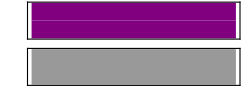

```mathematica
PlaySetChord[{1,2},1.2]
```